```mathematica
CC
```

所有临时定义已清空!

```mathematica
MultiFactorial[3k,3,Complex->True]
MultiFactorial[3k,3]
```

{Simplify→True,Complex→False}

1/(2 Gamma[1/3] Gamma[2/3])3^(1/3 (-5+3 k)) Gamma[1+k] (6 Gamma[1/3]+6 Cos[2/3 (1+3 k) π] Gamma[1/3]+6 Cos[4/3 (1+3 k) π] Gamma[1/3]+6 3^(1/3) Gamma[2/3]-3 3^(1/3) Cos[4 k π] Gamma[2/3]+6 3^(1/3) Cos[2/3 (2+3 k) π] Gamma[2/3]+2 3^(2/3) Gamma[1/3] Gamma[2/3]+2 3^(2/3) Cos[2 k π] Gamma[1/3] Gamma[2/3]+2 3^(2/3) Cos[4 k π] Gamma[1/3] Gamma[2/3]-3 3^(5/6) Gamma[2/3] Sin[4 k π])

3^Quotient[2+3 k,3] Binomial[k,Quotient[2+3 k,3]] Quotient[2+3 k,3]!

3^Quotient[1+3 k,3] Binomial[1/3 (-1+3 k),Quotient[1+3 k,3]] Quotient[1+3 k,3]!

```mathematica
HyperFactorial[n_]:=Hyperfactorial[n]
SuperFactorial[n_]:=BarnesG[n+2]
SubFactorial[n_]:= Subfactorial[n]
```

```mathematica
Table[SuperFactorial[n],{n,10}]//TT
Table[Product[k!,{k,n}],{n,10}]//TT
```

总运行时:  0.00054724

CPU 时间:  0.

{1,2,12,288,34560,24883200,125411328000,5056584744960000,1834933472251084800000,6658606584104736522240000000}

总运行时:  0.0000713792

CPU 时间:  0.

{1,2,12,288,34560,24883200,125411328000,5056584744960000,1834933472251084800000,6658606584104736522240000000}

```mathematica
RisingFactorial[x_,n_]:=Pochhammer[x,n]

MakeBoxes[RisingFactorial[z_Symbol,n_],TraditionalForm]:=SuperscriptBox[MakeBoxes[z,TraditionalForm],MakeBoxes[OverBar@n,TraditionalForm]]
MakeBoxes[RisingFactorial[z_,n_],TraditionalForm]:=SuperscriptBox[RowBox[{"(",MakeBoxes[z,TraditionalForm],")"}],MakeBoxes[OverBar@n,TraditionalForm]]

RisingFactorial[x+1,n]//HoldForm//TraditionalForm
```

(x+1)^(n̄)

```mathematica
D[RisingFactorial[x,n],x]
```

Pochhammer[x,n] (-PolyGamma[0,x]+PolyGamma[0,n+x])

```mathematica
FallingFactorial[x_, n_] := (-1)^n Pochhammer[-x, n]
MakeBoxes[FallingFactorial[z_Symbol,n_],TraditionalForm]:=SuperscriptBox[MakeBoxes[z,TraditionalForm],MakeBoxes[Style[n,Underlined],TraditionalForm]]
MakeBoxes[FallingFactorial[z_,n_],TraditionalForm]:=SuperscriptBox[RowBox[{"(",MakeBoxes[z,TraditionalForm],")"}],MakeBoxes[Style[n,Underlined],TraditionalForm]]
RSolve[{x a[x,n]==a[x,n+1]+n a[x,n],a[x,0]==1},a[x,n],n]
FallingFactorial[x,n]//HoldForm//TraditionalForm


RisingFactorial[x,0]
```

{{a[x,n]→(-1)^(1+n) x Pochhammer[1-x,-1+n]}}

x^n

RisingFactorial[x,0]

```mathematica
ExpFactorial[0]:=1
ExpFactorial[n_]:=ExpFactorial[n]=n^(ExpFactorial[n-1])
RSolve[{a[n]==n^a[n-1],a[1]==1},a[n],n]
```

```mathematica
超几何函数
```

```mathematica
Format[Hypergeometric1F1Regularized[a,b,c],TraditionalForm]//MakeBoxes
```

TagBox[FormBox[TemplateBox[{a,b,c},Hypergeometric1F1Regularized],TraditionalForm],#1&]

```mathematica
CC
AppendTo[$Path,DirectoryName@NotebookFileName[]];
Needs["Tschirnhaus`"]
```

```mathematica
D[LogGamma[x],x]
```

```mathematica
AlternatingFactorial[n]
```

```mathematica
Bernoulli[x_]:=Gamma[x]
Hadamard[x_]:=(PolyGamma[1-x/2]-PolyGamma[1/2-x/2])/(2Gamma[1-x])
Luschny[x_]:=(1/2+x(PolyGamma[1-x/2]-PolyGamma[1/2-x/2])/2)/(-x)!
```

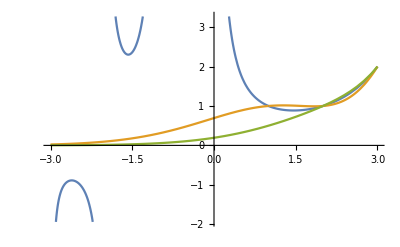

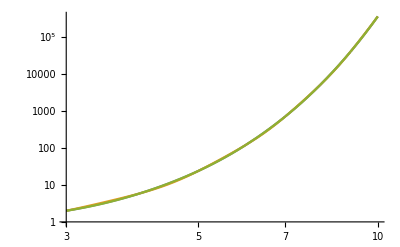

```mathematica
Plot[{Bernoulli[x],Hadamard[x],Luschny[x-1]},{x,-3,3}]
LogLogPlot[{Bernoulli[x],Hadamard[x],Luschny[x-1]},{x,3,10}]
```

```mathematica
Lerch
```

```mathematica
n!//FunctionExpand
```

```mathematica
Gamma[1-n]==(-n)!
```

```mathematica
IntegerDigits[#,MixedRadix[Reverse@Range[2,Ceiling[InverseFunction[Factorial][1000]]]]]&[1000]
```

{1,2,1,2,2,0}

```mathematica
AlternatingFactorial
```

```mathematica
反函数
```

5

```mathematica
{Bernoulli[x],Hadamard[x],Luschny[x-1]}/.x->3/2//FullSimplify
```

{(√π)/2,(4+π)/(4 √π),(2+π)/(4 √π)}

```mathematica
7^n*Gamma[n+1/7]/Gamma[1/7]
```

(7^n Gamma[1/7+n])/Gamma[1/7]

```mathematica
Table[(2^n Gamma[1/2+n])/Gamma[1/2],{n,1,20}]//FullSimplify
```

{1,3,15,105,945,10395,135135,2027025,34459425,654729075,13749310575,316234143225,7905853580625,213458046676875,6190283353629375,191898783962510625,6332659870762850625,221643095476699771875,8200794532637891559375,319830986772877770815625}

```mathematica
Table[Factorial2[n],{n,1,20}]
```

{1,2,3,8,15,48,105,384,945,3840,10395,46080,135135,645120,2027025,10321920,34459425,185794560,654729075,3715891200}

```mathematica
ComplexFnPlot[f_,range_,options___]:=Block[{rangerealvar,rangeimagvar,g},g[r_,i_]:=(f/.range[[1]]:>r+I i);
Plot3D[Abs[g[rangerealvar,rangeimagvar]],{rangerealvar,Re[range[[2]]],Re[range[[3]]]},{rangeimagvar,Im[range[[2]]],Im[range[[3]]]},options,ColorFunction->(Hue[Mod[Arg[g[#1,#2]]/(2*Pi)+1,1]]&),ColorFunctionScaling->False]]
ComplexFnPlot[Gamma[z],{z,-3.5-3.5I,3.5+5.5I},PlotRange->{0,4}]
```

-Graphics3D-

```mathematica
ComplexFnPlot[Bernoulli[z],{z,-3.5-5.5I,10+5.5I},ScalingFunctions->"Log"]
ComplexFnPlot[Hadamard[z],{z,-3.5-5.5I,10+5.5I},ScalingFunctions->"Log"]
ComplexFnPlot[Luschny[z-1],{z,-3.5-5.5I,10+5.5I},ScalingFunctions->"Log"]
```

-Graphics3D-

-Graphics3D-

-Graphics3D-

```mathematica
With[{pr=FoldList[Times,1,Prime@Range[20]]},Table[pr[[PrimePi[n]+1]],{n,0,40}]]
```

{1,1,2,6,6,30,30,210,210,210,210,2310,2310,30030,30030,30030,30030,510510,510510,9699690,9699690,9699690,9699690,223092870,223092870,223092870,223092870,223092870,223092870,6469693230,6469693230,200560490130,200560490130,200560490130,200560490130,200560490130,200560490130,7420738134810,7420738134810,7420738134810,7420738134810}

```mathematica
Primorial[0]:=1
Primorial[1]:=2
Primorial[n_]:=Primorial[n]=Prime[n]Primorial[n-1]
```

```mathematica
Series[Prime[n],{n,1,2}]
```

2+Prime'[1] (n-1)+1/2 Prime''[1] (n-1)^2+O[n-1]^3

```mathematica
fastPrime[n_]:=n(Log[n]+Log[Log[n]]-1+(Log[Log[n]]-2)/Log[n]-(Log[Log[n]]^2-6 Log[Log[n]]+11)/(2 Log[n]^2))
```